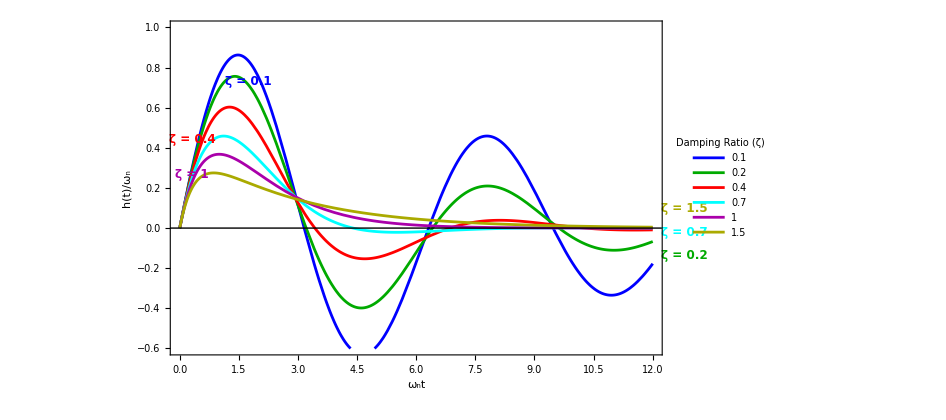

```mathematica
(*1. 定义归一化单位脉冲响应函数 h(t)/wn*)normalizedImpulseResponse[τ_,ζ_]:=Which[0<=ζ<1,(1/Sqrt[1-ζ^2]) Exp[-ζ τ] Sin[Sqrt[1-ζ^2] τ],ζ==1,τ Exp[-τ],ζ>1,(1/Sqrt[ζ^2-1]) Exp[-ζ τ] Sinh[Sqrt[ζ^2-1] τ]];

(*2. 设置图中对应的阻尼比参数*)
zetaList={0.1,0.2,0.4,0.7,1,1.5};
colors={Blue,Darker[Green],Red,Cyan,Darker[Magenta],Darker[Yellow]};

(*3. 绘图*)
Plot[Evaluate[Table[normalizedImpulseResponse[τ,z],{z,zetaList}]],{τ,0,12},PlotRange->{{0,12},{-0.6,1}},PlotStyle->colors,Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(ω\), \(n\)]\)t",14,Italic],Style["h(t)/\!\(\*SubscriptBox[\(ω\), \(n\)]\)",14,Italic]},GridLines->{None,{0}},GridLinesStyle->Directive[Black,AbsoluteThickness[1]],ImageSize->700,AspectRatio->0.6,PlotLabels->Placed[Map[Style[Row[{"ζ = ",#}],12,Bold,colors[[Position[zetaList,#][[1,1]]]]]&,zetaList],{Scaled[0.2],After}],PlotLegends->LineLegend[zetaList,LegendLabel->"Damping Ratio (ζ)"]]
```

```mathematica
Manipulate[Plot[Which[0<ζ<1,(1/Sqrt[1-ζ^2]) Exp[-ζ τ] Sin[Sqrt[1-ζ^2] τ],ζ==1,τ Exp[-τ],ζ>1,(1/Sqrt[ζ^2-1]) Exp[-ζ τ] Sinh[Sqrt[ζ^2-1] τ]],{τ,0,15},PlotRange->{{0,15},{-0.6,1}},PlotStyle->{Thick,Blue},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(ω\), \(n\)]\)t",14],Style["h(t)/\!\(\*SubscriptBox[\(ω\), \(n\)]\)",14]},GridLines->{Automatic,{0}},PlotLabel->Style[Row[{"当前阻尼比 ζ = ",ζ}],16,Bold],Exclusions->None],(*定义滑块范围：从 0.05 到 2.0，步长 0.05*){ζ,0.05,2.0,0.05,Appearance->"Labeled"}]
```